```mathematica
ClearAll["Global`*"];
```

# Static axis symmetric piece Psi2 and Psi4 calculation for Kerr spacetime

```mathematica
(*Define Spin weight -2 spherical harmonics*)
```

```mathematica
dlms[l_, m_, s_, θ_]:=√((l+m)!(l-m)!(l+s)!(l-s)!)Sum[(-1)^k(Sin[θ/2]^(2 k + s -m)Cos[θ/2]^(2 l + m -s-2k))/(k!(l+m-k)!(l-s-k)!(s-m+k)!), {k, Max[0, m-s], Min[l+m, l-s]}]
```

```mathematica
sYlm[l_, m_, s_, θ_, ϕ_]:= (-1)^s √((2 l+1)/(4π)) dlms[l, m, s, θ]Exp[I m ϕ]
```

```mathematica
(*Conserved energy and angular momentum of particle on circular orbit*)
```

```mathematica
Enrg[mu_, M_,r_ ]:= mu(1-2M/r)(1-3M/r)^(-1/2)
Lorb[mu_, M_,r_ ]:= mu(r M)^(1/2)(1-3M/r)^(-1/2)
```

```mathematica
Delta[r_, M_]:= r(r- 2 M)
LambdaS[l_, s_] :=(l+s)!/(l-s)!
```

```mathematica
sl0[r_,θ_,M_,En_, L_, l_]:= ((π En)/Delta[r, M](D[D[sYlm[l, 0, -2, x, ϕ], x], x] - 2 sYlm[l, 0, -2, x, ϕ]) - (4π I L)/r^3  D[sYlm[l, 0, -2, x, ϕ], x])/. x-> θ
sl1[r_,θ_,M_,En_, L_, l_]:= ( - (2π I L)/r^2  D[sYlm[l, 0, -2, x, ϕ], x]-(2π M  En)/Delta[r, M] sYlm[l, 0, -2, x, ϕ])/. x-> θ
sl2[r_,θ_,M_,En_, L_, l_]:= (-(π M r En)/Delta[r, M]( sYlm[l, 0, -2, x, ϕ]))/. x-> θ
```

```mathematica
Rml[r_, l_, M_ ]:= (M ((l+2)!)/((l-2)!))^(-1/2)Delta[r, M]LegendreP[l,2, r/M-1]
Rpl[r_, l_, M_ ]:= (M ((l+2)!)/((l-2)!))^(-1/2)Delta[r, M]LegendreQ[l,2, r/M-1]
```

```mathematica
Cpl[r_,θ_,M_,En_, L_, l_]:= (-sl0[r,θ,M,En, L, l]Rml[r, l, M] + sl1[r,θ,M,En, L, l]D[Rml[s, l, M],s] -  sl1[r,θ,M,En, L, l]D[D[Rml[s, l, M],s],s])/.s-> r
Cml[r_,θ_,M_,En_, L_, l_]:= (-sl0[r,θ,M,En, L, l]Rpl[r, l, M] + sl1[r,θ,M,En, L, l]D[Rpl[s, l, M],s] -  sl1[r,θ,M,En, L, l]D[D[Rpl[s, l, M],s],s])/.s-> r
```

```mathematica
(*Defining Psi4lSAS*)
```

```mathematica
Psi4lp[r_, r0_, l_, M_, mu_]:= Cpl[r0,π/2,M,Enrg[mu, M,r0], Lorb[mu, M,r0], l]Rpl[r, l, M]
Psi4lm[r_, r0_, l_, M_, mu_]:= Cml[r0,π/2,M,Enrg[mu, M,r0], Lorb[mu, M,r0], l]Rml[r, l, M]
```

```mathematica
Psi4SASp[r_,r0_, M_, mu_, θ_, lmax_]:= r^-4 Sum[Psi4lp[r, r0, l, M, mu]sYlm[l, 0, -2, θ, ϕ], {l, 2, lmax}]
```

```mathematica
(*Defining Psi2*)
```

```mathematica
Psi2[r_, θ_, r0_, lmax_, M_, mu_]:= ( 2 Sum[(((l+2)!)/((l-2)!))^(-1/2)D[Psi4lp[x, r0, l, M, mu]/x^2, x], {l, 2, lmax}])/.x-> r
```

0.0000378422

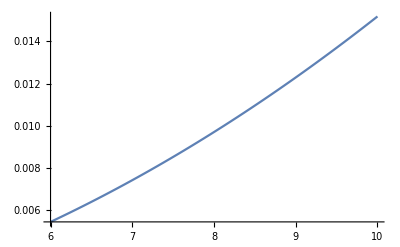

```mathematica
Plot[100 Re[Psi4SASp[100,r, 0.01, 1, π/2, 3]//N], {r, 6, 10}]
```